#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_ThinFilm.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

/home/juanathan/Documents/Wolfram/Wolfram_scripts

```mathematica
fs = 11;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

## Pruebas

### Fresnel Limits Sphere

0.

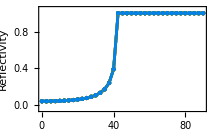
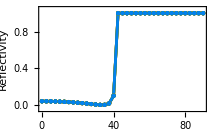

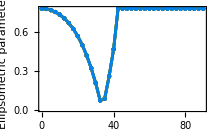
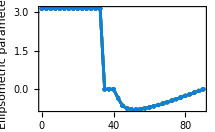

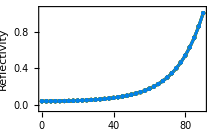
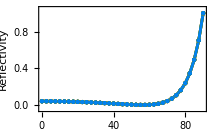

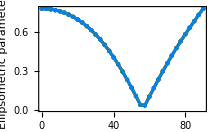
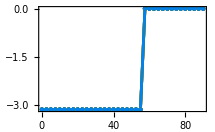

```mathematica
(*
Sin partpículas Θ = 0
Esferas de algún material absobente Subscript[ε, p]= 1 + i 2, en aire sobre vidrio
Incidencia por vidrio a aire -> ATR
Incidencia pór aire a vidrio
*)
a = 25; 
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.0/(Pi*a*a)

epsilon = Transpose[Table[{1., 1.+2*I, 1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,a,cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data

data = ThinFimlElipsometryInt[ang,epsilon,lda,a,cfrac];
ListLinePlot[Transpose[#],PlotRange->Automatic,DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Ellipsometric parameters"})]& /@ data
  
epsilon = Transpose[Table[{1.5,1.+2*I,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,a,cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
data = ThinFimlElipsometryInt[ang,epsilon,lda,a,cfrac];
ListLinePlot[Transpose[#],PlotRange->Automatic,DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Ellipsometric parameters"})]& /@ data
```

```mathematica
(*
Con partpículas Θ = 0.15
Esferas del mismo material que de la matriz: primero matriz de aire (esferas de aire) incidienci por vidrio -> ATR
Esferas del mismo material que de la matriz: primero matriz de vidrio (esferas de viddrio) incidienci por aire -
*)
a = 25;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.16/(Pi*a*a)

epsilon = Transpose[Table[{1.,1.,1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,a,cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,1.5,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,a,cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

0.0000814873

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

### Fresnel Limits Ellipsoid

```mathematica
(*
Sin partpículas Θ = 0
Esferas de algún material absobente Subscript[ε, p]= 1 + i 2, en aire sobre vidrio
Incidencia por vidrio a aire -> ATR
Incidencia pór aire a vidrio
*)
a = 25; b = 20;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.0/(Pi*a*a)

epsilon = Transpose[Table[{1., 1.+2*I, 1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,1.+2*I,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

0.

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
(*
Con partpículas Θ = 0.15
Esferas del mismo material que de la matriz: primero matriz de aire (esferas de aire) incidienci por vidrio -> ATR
Esferas del mismo material que de la matriz: primero matriz de vidrio (esferas de viddrio) incidienci por aire -
*)
a = 25; b = 20;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.16/(Pi*a*a)

epsilon = Transpose[Table[{1.,1.,1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,1.5,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

0.0000814873

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

### Gold Au

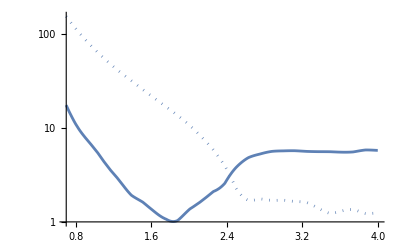

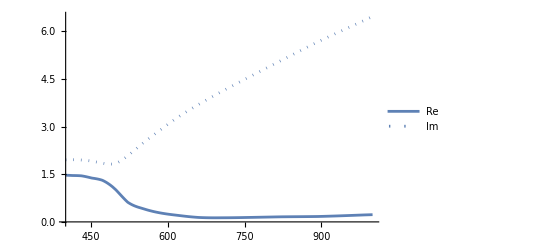

```mathematica
ReImPlot[-I*JohnsonChristyAuRef[hcPlanckSpeed/x]^2,{x,.7,4},ScalingFunctions->"Log"]
ReImPlot[JohnsonChristyAuRef[x],{x,400,1000},PlotLegends->"ReIm"]
```

```mathematica
a = 50.2;
cfrac = 0.16/(Pi*a*a)
cfrac = 19.8*^-6
```

0.0000202098

0.0000198

0.0000202098

0.0000198

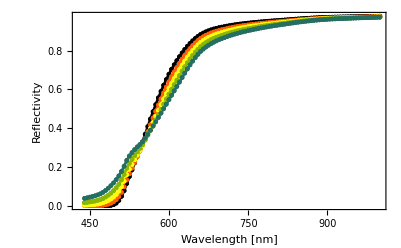
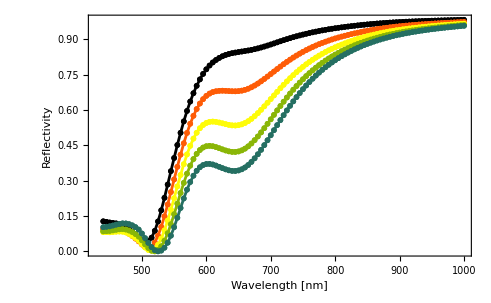

```mathematica
a = 80.2; b = 38.1;
lda = Range[440,1000,5.];
ang = Range[65,73,2.]*Pi/180.;
cfrac = 0.16/(Pi*a*a)
cfrac = 19.8*^-6

epsilon = Transpose[Table[{1.3328,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```

0.0000202098

0.0000198

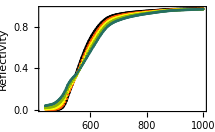
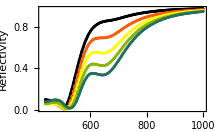

```mathematica
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_ThinFilm.wls"

a = 50.2; b = 40.1;
lda = Range[440,1000,5.];
ang = Range[65,73,2.]*Pi/180.;
cfrac = 0.16/(Pi*a*a)
cfrac = 19.8*^-6

epsilon = Transpose[Table[{1.3328,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```

7.91811×10^-6

0.0000198

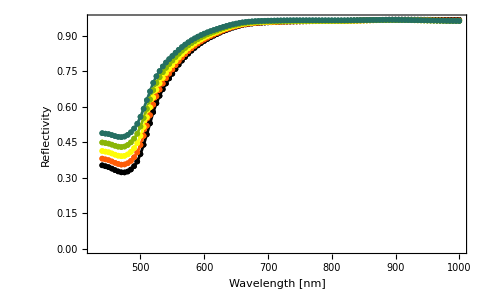
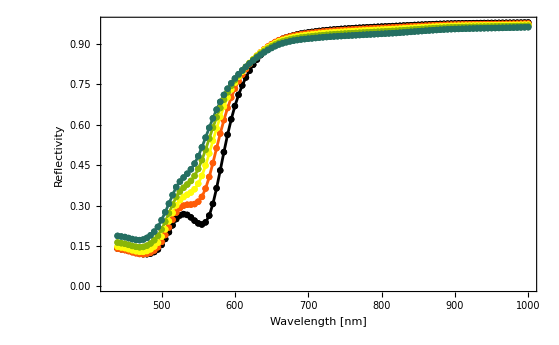

```mathematica
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_ThinFilm.wls"

a = 80.2; b = 40.1;
lda = Range[440,1000,5.];
ang = Range[65,73,2.]*Pi/180.;
cfrac = 0.16/(Pi*a*a)
cfrac = 19.8*^-6

epsilon = Transpose[Table[{1.3328,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```

0.0000203718

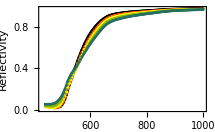
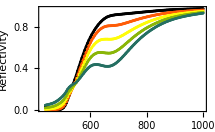

```mathematica
a = 50; b = 49;
lda = Range[440,1000,5.];
ang = Range[65,73,2.]*Pi/180.;
cfrac = 0.16/(Pi*a*a)

epsilon = Transpose[Table[{1.3328,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```

0.0000203718

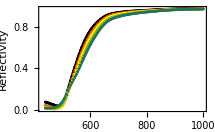
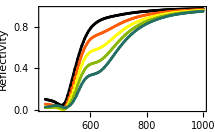

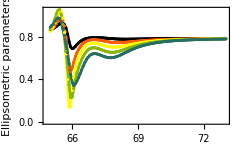
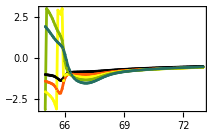

```mathematica
a = 50; 
lda = Range[440,1000,5.];
ang = Range[65,73,2.]*Pi/180.;
cfrac = 0.16/(Pi*a*a)

epsilon = Transpose[Table[{1.3328,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,a,cfrac]&, {ThinFilmReflectionIntS,ThinFilmReflectionIntP}];
ListLinePlot[#,DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
data = ThinFimlElipsometryInt[ang,epsilon,lda,a,cfrac];
ListLinePlot[#,PlotRange->All,DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Ellipsometric parameters"})]& /@ data
```